```mathematica
Directory[]
Cv=Import["Cv","Table"]
```

/home/ponadto/Desktop/backup/backup/md5Dec/hp/plikiDlaStudentow/SA_default_1.0-0.1

{{1.,0.96528},{0.95,1.2295},{0.9,1.44136},{0.85,1.7504},{0.8,1.75367},{0.75,2.75186},{0.7,2.64629},{0.65,3.95707},{0.6,4.149},{0.55,4.3676},{0.5,4.97392},{0.45,11.1743},{0.4,14.002},{0.35,20.1303},{0.3,24.0599},{0.25,15.4008},{0.2,0.},{0.15,0.}}

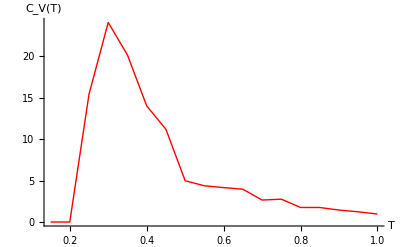

```mathematica
ListPlot[Cv,Joined->True,PlotStyle->{Red,Thick},AxesLabel->{"T","C_V(T)"}]
```

```mathematica
gyr=Import["meanGyr","Table"]
```

{{1.,174.579},{0.95,170.941},{0.9,169.503},{0.85,170.643},{0.8,173.992},{0.75,162.315},{0.7,163.91},{0.65,159.432},{0.6,154.045},{0.55,149.553},{0.5,138.983},{0.45,133.537},{0.4,125.053},{0.35,104.555},{0.3,97.8726},{0.25,72.3812},{0.2,66.},{0.15,66.}}

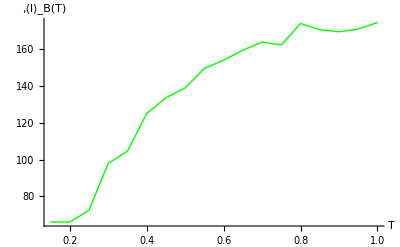

```mathematica
ListPlot[gyr,Joined->True,PlotStyle->{Green,Thick},AxesLabel->{"T",",⟨I⟩_B(T)"},AxesOrigin->{0,60}]
```

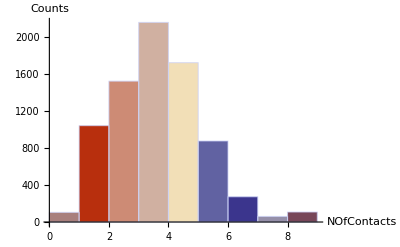

{1,2,3,4,5}

```mathematica
ktoryHistogram="hist0.45";
hist=Import[ktoryHistogram,"Table"];
doHistogramu=Flatten[Table[Table[i,{j,1,hist⟦i+1,2⟧}],{i,0,Length[hist]-1}]];
Histogram[doHistogramu,AxesLabel->{"NOfContacts","Counts"},ChartStyle->13]
```